# Linear Regression

Whenever we perform a linear regression on some data, we might get carried away by good values of R^2 or p. However, such single valued quantities don’t tell the whole story.

## Temperature Model

We will create a model that is a function of temperature:

```mathematica
c = RandomReal[{0,25}];
y = RandomReal[{0,100}];
M[T_]:= c T + y;
```

We will now add random noise to the model:

```mathematica
Nsamples = 250;
Tsamples = RandomReal[{0,100}, Nsamples]//Sort;
noise = 25;
Msamples = (M/@Tsamples)+RandomVariate[NormalDistribution[0,noise c],Nsamples];
```

```mathematica
MTdata = Riffle[Tsamples, Msamples] //Partition[#,2]&;
```

## Linear Fit of the Data

We will use the Mathematica’s built-in fitting to do a standard linear-regression:

```mathematica
lm = LinearModelFit[MTdata,x,x];
```

```mathematica
{py,pc} = CoefficientList[Normal[lm],x]
```

{103.446,19.0562}

## Residuals vs Fitted Values

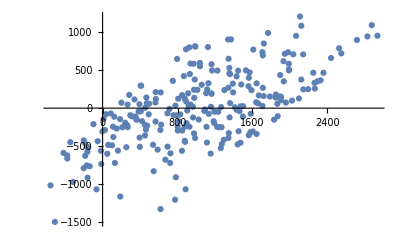

```mathematica
fvals = lm/@Tsamples;
res = Msamples-fvals;
ListPlot[Transpose[{Msamples,res}]]
```

So the lm[“FitResiduals”] does the same thing as our function above that found the residuals.

## Quantile Plots

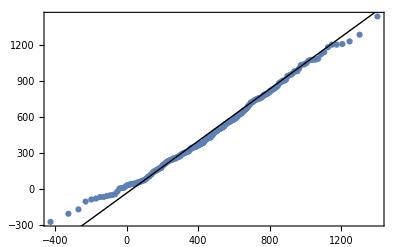

```mathematica
QuantilePlot[Msamples]
```

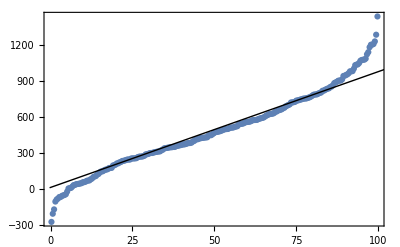

```mathematica
QuantilePlot[Msamples,UniformDistribution[{0,100}]]
```

## Spread - Location Plot

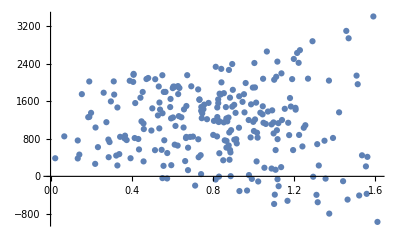

```mathematica
ListPlot[Riffle[Sqrt[Abs[lm["StandardizedResiduals"]]],Msamples]//Partition[#,2]&]
```

## Residuals vs Leverage

```mathematica
influence = Riffle[lm["HatDiagonal"],lm["StandardizedResiduals"]]//Partition[#,2]&;
cooks = Riffle[lm["CookDistances"],lm["StandardizedResiduals"]]//Partition[#,2]&;
```

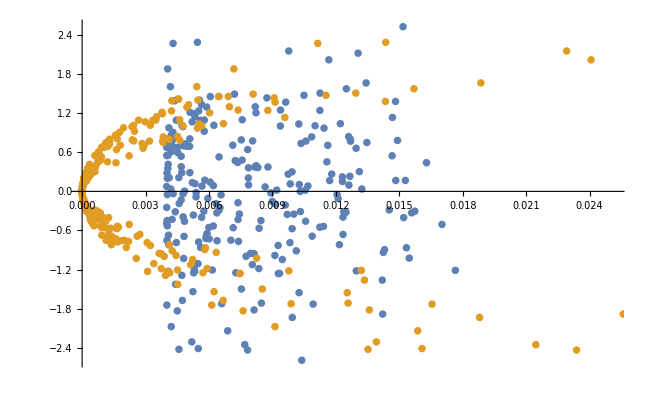

```mathematica
ListPlot[{influence,cooks},ImageSize->650]
```